```mathematica
dataPath = "../data/2017/MessexperimentGeschwindigkeitenSS2017.csv";
data= SemanticImport@FileNameJoin@{NotebookDirectory[],dataPath};
```

```mathematica
längeEbene = 27.3;
längeTreppe = :9.39;
```

```mathematica
dataAuf = data[Select[#Treppe == "auf"&], <|
"id"->"ID Proband", 
"runde"->"Runde",
"bemerkung"-> "Bemerkung",
 "vAuf"->(längeTreppe/#"Zeit in sec"&)
|>];
dataAb = data[Select[#Treppe == "ab"&], <|
"id"->"ID Proband", 
"runde"->"Runde",
"bemerkung"-> "Bemerkung",
 "vAb"->(längeTreppe/#"Zeit in sec"&)
|>];
dataEbene = data[Select[#Ebene == "x"&], <|
"id"->"ID Proband", 
"runde"->"Runde",
"bemerkung"-> "Bemerkung",
 "vEbene"->(längeEbene/#"Zeit in sec"&)
|>];

abauf = JoinAcross[dataAuf, dataAb, {"id","runde"}];
gesamt = JoinAcross[abauf,dataEbene, {"id","runde"}];
```

```mathematica
a = Normal@Values@gesamt[Select[#bemerkung==""&],{"vAuf","vEbene"}];
gesamt[Select[#bemerkung!=""&]]
```

Dataset[<>]

FittedModel[0.445889+0.595819 x]

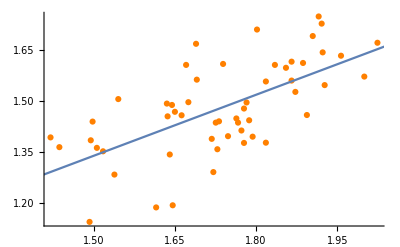

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.408107 | 0.408107 | 36.6727 | 1.57165×10^-7
Error | 52 | 0.578674 | 0.0111283 |  | 
Total | 53 | 0.986781 |  |  |

```mathematica
lm = LinearModelFit[a,{x},{x}]
Show[ListPlot[lm["Data"],PlotStyle->Orange],Plot[lm[x],{x,0,100}]]
lm["ANOVATable"]
```